Load the JSON file.  What we get is a recursive set of replacement rules.
The keys are strings.

```mathematica
jfile =Import["c:\\git\\FusorExperiments\\logs\\keep\\fusor-2021-05-24T23-34-10-332Z_attempt 3.json"]
```

{base-timestamp→1621899250328,instant→2021-05-24T23:34:10.332Z,log→{{device→<reset>,data→{},servertime→1621899250328},{device→RP,data→{rp_in→{value→False,vartime→0},devicetime→1625162},servertime→1621899250332},272101,{}}}
 |  |  |  |

```mathematica
ListDevices[jfile_List]:=Module[{log},
log="log"/.jfile;
Select[DeleteDuplicates[("device"/.#)&/@log],#≠"device"&]
]
```

```mathematica
ListDevices[jfile]
```

{<reset>,RP,HV-LOWSIDE,HV-RELAY,GAS,VARIAC,SENSORARRAY,TMP,PIRANI,Heartbeat,Command,Comment}

```mathematica
GetDeviceLog[deviceName_String,jfile_List]:=Module[{log},
log="log"/.jfile;
Select[log,("device"/.#)==deviceName&]
]
```

```mathematica
getVar[s_String,deviceLog_List,timeFit_FittedModel]:=
Module[{dList,vList},
dList=("data"/.#)& /@ deviceLog;
vList = Select[(s/.#)& /@ dList,Head[#]==List&];
{timeFit @("vartime"/.#), ("value"/.#)}& /@ vList
]
```

```mathematica
getAllVars[deviceLog_List,timeFit_FittedModel]:=
Module[{varList,dlist},
dlist=("data"/.#)& /@ deviceLog;
varList=Union[Table[i[[1]],{i,Select[Flatten[dlist],Head[#[[2]]]==List&]}]];
{varList,Table[DeleteDuplicates[getVar[v,deviceLog,timeFit]],{v,varList}]}
]
```

```mathematica
GetDeviceData[deviceName_String,jfile_List]:=Module[{log,dev,baseServerTime,timeFit,devServerTimes,deviceTimes},
{log,baseServerTime}={"log","base-timestamp"}/.jfile;
dev=Select[log,("device"/.#)==deviceName&];
devServerTimes=("servertime"/.#&/@dev)-baseServerTime;
deviceTimes="devicetime"/.("data"/.#)&/@dev;
timeFit = LinearModelFit[Transpose[{deviceTimes,devServerTimes}],x,x,WorkingPrecision->13];
getAllVars[dev,timeFit]
]
```

```mathematica
GetTimeFit[deviceName_String,jfile_List]:=Module[{log,dev,baseServerTime,timeFit,devServerTimes,deviceTimes},
{log,baseServerTime}={"log","base-timestamp"}/.jfile;
dev=Select[log,("device"/.#)==deviceName&];
devServerTimes=("servertime"/.#&/@dev)-baseServerTime;
deviceTimes="devicetime"/.("data"/.#)&/@dev;
timeFit = LinearModelFit[Transpose[{deviceTimes,devServerTimes}],x,x,WorkingPrecision->13]
]
```

```mathematica
GetRange[x_List,t1_,t2_]:=Select[x,#[[1]]>t1&&#[[1]]<t2&];
```

```mathematica
piraniTimeFit=GetTimeFit["PIRANI",jfile]
```

FittedModel[-1.624582902×10^6+1.001001988 x]

```mathematica
command4TimeFit=GetTimeFit["Command",jfile4]
```

FittedModel[-1.622165129349×10^12+1. x]

```mathematica
pirani4TimeFit=GetTimeFit["PIRANI",jfile4]
```

FittedModel[-87899.25576432+1.001006947267 x]

```mathematica
piraniData=GetDeviceData["PIRANI",jfile];
```

```mathematica
piraniData
```

{{p2,p3,p4},{{{-157.88,-28.3},{184.47,-28.3},{522.804,-28.3},{854.136,-28.3},5135,{1.7587918×10^6,-758.},{1.75913315×10^6,-758.},{1.75947449×10^6,-758.}},{1},{1}}}
 |  |  |  |

```mathematica
hvData=GetDeviceData["HV-LOWSIDE",jfile];
```

```mathematica
hvData
```

{{cw_avg,n,nst_rms,variac_rms},{{{7.157,-0.0198334},{126.13,-0.0115432},{244.1,-0.0143069},14805,{1.75917643×10^6,-0.106878},{1.7592954×10^6,-0.11724},{1.75941437×10^6,-0.0999693}},{1},1,{1}}}
 |  |  |  |

```mathematica
variacData=GetDeviceData["VARIAC",jfile];
```

```mathematica
variacData
```

{{dial_volts,input_volts,stop},{{{-66237.966,0},{5101.599,1},{5194.599,1},{14665.54,5},{14741.54,5},{23159.49,6},{23329.49,6},{45950.351,7},{46103.35,7},{390689.25,8},{390807.249,8},{418074.083,9},{418120.082,9},{1.68284737×10^6,0},{1.68361637×10^6,0}},{{-67018.961,0},{5082.6,1},{5190.599,1},{14601.54,5},{14737.54,5},{23140.49,6},{23325.49,6},{45929.351,7},{46099.35,7},{390670.25,8},{390803.249,8},{418055.083,9},{418116.082,9},{1.68360637×10^6,0}},{{-1.625296464×10^6,0}}}}

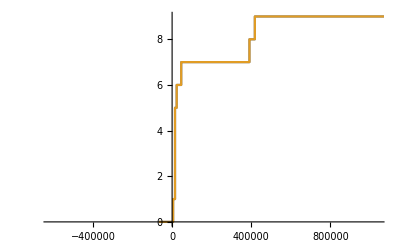

```mathematica
ListStepPlot[variacData[[2]]]
```

```mathematica
hvData[[1]]
```

{cw_avg,n,nst_rms,variac_rms}

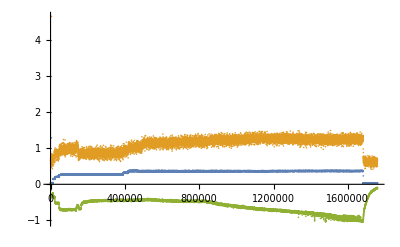

```mathematica
ListPlot[{hvData[[2,3]],hvData[[2,4]],hvData[[2,1]]}]
```

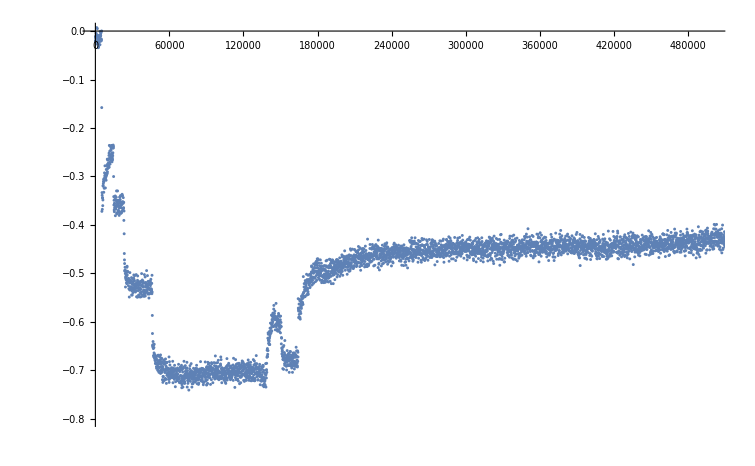

```mathematica
ListPlot[hvData[[2,1]],PlotRange->{{0,500000},{-.8,0}}]
```

```mathematica
piraniData[[1]]
```

{p2,p3,p4}

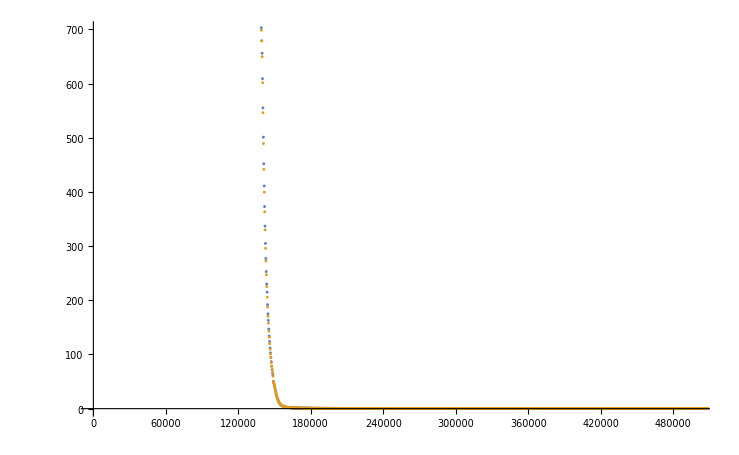

```mathematica
ListPlot[piraniData[[2,2;;3]],PlotRange->{{0,500000},{0,700}}]
```

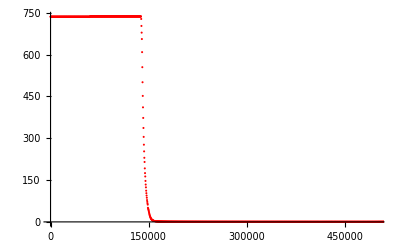

```mathematica
ListPlot[piraniData[[2,2]],PlotRange->{{0,500000},All},PlotStyle->Red]
```

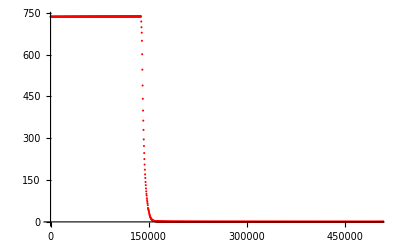

```mathematica
ListPlot[piraniData[[2,3]],PlotRange->{{0,500000},All},PlotStyle->Red]
```

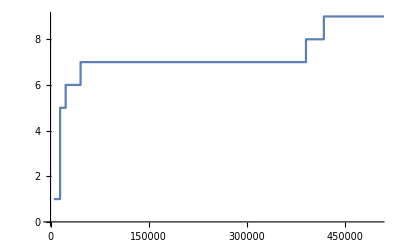

```mathematica
ListStepPlot[DeleteDuplicates[variacData[[2,1]]],PlotRange->{{0,500000},All}]
```

```mathematica
piraniFlat=Flatten[piraniData[[2]],{{2},{1,3}}];
```

```mathematica
Export["c:\\temp\\pirani.csv",piraniFlat]
```

c:\temp\pirani.csv

```mathematica
command=GetDeviceData["Command",jfile];
```

```mathematica
command4=GetDeviceData["Command",jfile4];
```

```mathematica
command[[1]]
```

{ip,observer,text}

```mathematica
MatrixForm[command4[[2,3]]]
```

(56336. | #promote: gfellows
66136. | RP on
72600. | RP off
85873. | Solenoid open
91331. | Set needle valve:50.0
91403. | Set needle valve:50.0
100370. | Set needle valve:100.0
100460. | Set needle valve:100.0
137610. | Solenoid closed
143650. | Set needle valve:0.0
143720. | Set needle valve:0.0
158540. | variac:set:1.0
158600. | variac:set:1.0
182440. | variac:set:5.0
182580. | variac:set:5.0
193220. | variac:set:11.0
193270. | variac:set:11.0
221180. | variac:set:0.0
221200. | variac:set:0.0
227510. | Solenoid open
231950. | Set needle valve:100.0
232030. | Set needle valve:100.0
292680. | Solenoid closed
297350. | Set needle valve:0.0
297400. | Set needle valve:0.0
306330. | variac:set:5.0
306390. | variac:set:5.0
327852. | variac:set:10.0
327882. | variac:set:10.0
347810. | RP on
379669. | TMP low
397384. | TMP on
440003. | TMP off
871341. | RP off)

```mathematica
jfile1 =Import["c:\\git\\FusorExperiments\\logs\\keep\\fusor-2021-05-25T00-13-02-020Z_repeat of success.json"];
```

```mathematica
jfile2 =Import["c:\\git\\FusorExperiments\\logs\\keep\\fusor-2021-05-25T00-45-51-491Z_tmp from plasma.json"];
```

```mathematica
jfile3 =Import["c:\\git\\FusorExperiments\\logs\\keep\\fusor-2021-05-25T01-14-29-433Z_repeat of tmp experiment.json"];
```

```mathematica
jfile4 =Import["c:\\git\\FusorExperiments\\logs\\keep\\fusor-2021-05-28T01-25-29-352Z_Paschen curve for 2000 V.json"];
```

```mathematica
ListDevices[jfile3]
```

{<reset>,PIRANI,HV-RELAY,TMP,GAS,RP,VARIAC,SENSORARRAY,HV-LOWSIDE,Heartbeat,Login,Command,<promote>,Comment}

```mathematica
GetTimeFit["PIRANI",jfile4]
```

FittedModel[-87899.25576432+1.001006947267 x]

```mathematica
GetTimeFit["HV-RELAY",jfile4]
```

FittedModel[-87255.87968506+0.999238581844 x]

```mathematica
GetTimeFit["TMP",jfile4]
```

FittedModel[-87206.00720662+0.9994128406443 x]

```mathematica
GetTimeFit["GAS",jfile4]
```

FittedModel[-88718.38015091+0.9999953155928 x]

```mathematica
GetTimeFit["RP",jfile4]
```

FittedModel[-87182.40129842+0.9991924431388 x]

```mathematica
GetTimeFit["VARIAC",jfile4]
```

FittedModel[-1.666184102181×10^6+0.9999832597302 x]

```mathematica
GetTimeFit["SENSORARRAY",jfile4]
```

FittedModel[-87894.34155473+1.001220802445 x]

```mathematica
GetTimeFit["HV-LOWSIDE",jfile4]
```

FittedModel[-87889.80213538+0.9997589316921 x]

```mathematica
name3="repeat of tmp experiment";
```

```mathematica
name4="Paschen Curve at 2000V";
```

```mathematica
rp1=GetDeviceData["RP",jfile1];
```

```mathematica
rp2=GetDeviceData["RP",jfile2];
```

```mathematica
rp3=GetDeviceData["RP",jfile3];
```

```mathematica
rp4=GetDeviceData["RP",jfile4];
```

```mathematica
rp4[[1]]
```

{rp_in}

```mathematica
rp1[[1]]
```

{rp_in}

```mathematica
tmp2=GetDeviceData["TMP",jfile2];
```

```mathematica
tmp3[[1]]
```

{error,lowspeed,pump_curr_amps,pump_freq,reset,tmp}

```mathematica
tmp3=GetDeviceData["TMP",jfile3];
```

```mathematica
MatrixForm[tmp3[[2,6]]]
```

(-49632.73338 | False
271374.116 | True
434451.581 | False)

```mathematica
MatrixForm[rp1[[2,1]]]
```

(-192297.5569 | False
138559.82 | True
150256.606 | False
154494.268 | True
157907.579 | False
161981.37 | True
388624.838 | False
1.71348821×10^6 | True)

```mathematica
MatrixForm[rp4[[2,1]]]
```

(-87182.4013 | False
66161.6646 | True
72625.4405 | False
347840.009 | True
871365.891 | False)

```mathematica
hv1=GetDeviceData["HV-LOWSIDE",jfile1];
```

```mathematica
hv2=GetDeviceData["HV-LOWSIDE",jfile2];
```

```mathematica
hv3=GetDeviceData["HV-LOWSIDE",jfile3];
```

```mathematica
hv4=GetDeviceData["HV-LOWSIDE",jfile4];
```

```mathematica
hv1[[1]]
```

{cw_avg,n,nst_rms,variac_rms}

```mathematica
hv2[[1]]
```

{cw_avg,n,nst_rms,variac_rms}

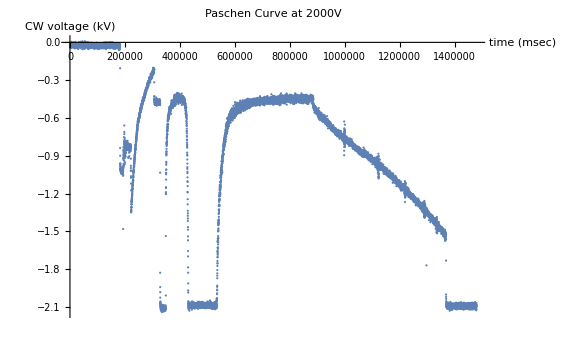

```mathematica
ListPlot[hv4[[2,1]],PlotLabel->name4,
AxesLabel->{"time (msec)","CW voltage (kV)"}]
```

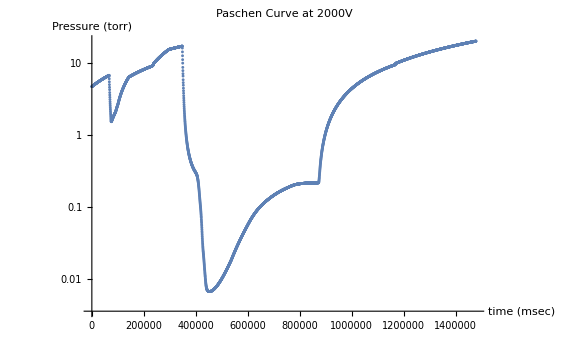

```mathematica
ListLogPlot[pirani4[[2,3]],PlotLabel->name4,
AxesLabel->{"time (msec)","Pressure (torr)"}]
```

```mathematica
hv4a=GetRange[hv4[[2,1]],330000,440000];
```

```mathematica
hv4b=GetRange[hv4[[2,1]],440000,1460000];
```

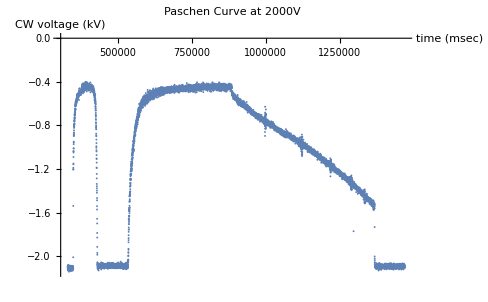

```mathematica
ListPlot[hv4a,PlotLabel->name4,
AxesLabel->{"time (msec)","CW voltage (kV)"}]
```

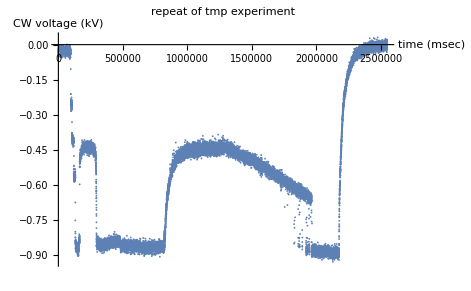

```mathematica
ListPlot[hv3[[2,1]],PlotLabel->name3,
AxesLabel->{"time (msec)","CW voltage (kV)"}]
```

```mathematica
hv3a=GetRange[hv3[[2,1]],271375,1240000];
```

```mathematica
hv3b=GetRange[hv3[[2,1]],1250000,2100000];
```

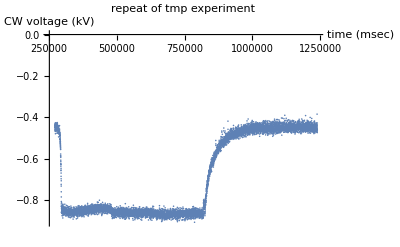

```mathematica
ListPlot[hv3a,PlotLabel->name3,
AxesLabel->{"time (msec)","CW voltage (kV)"}]
```

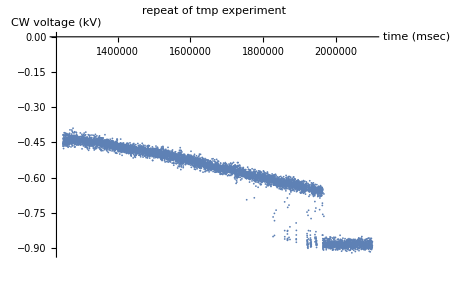

```mathematica
ListPlot[hv3b,PlotLabel->name3,
AxesLabel->{"time (msec)","CW voltage (kV)"}]
```

```mathematica
pv3b=Table[{intPressure3[x[[1]]],-x[[2]]},{x,hv3b}];
```

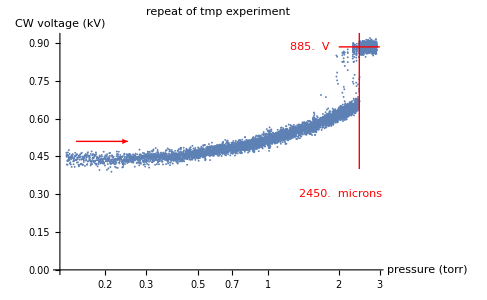

```mathematica
lp3b=ListPlot[pv3b, ScalingFunctions->{"Log",None},
Epilog->{Directive[{Red}],
p3=2.45;Line[{{Log[p3],0.4},{Log[p3],1.1}}],
v2=.885;Line[{{Log[2],v2},{Log[3],v2}}],
Text[1000 p3" microns",{Log[p3/1.2],0.3}],

Text[1000 v2" V",{Log[1.5],v2}],
Directive[Thick],
Arrow[{{Log[.15],0.51},{Log[.25],0.51}}]},
PlotLabel->name3,
AxesLabel->{"pressure (torr)","CW voltage (kV)"}]
```

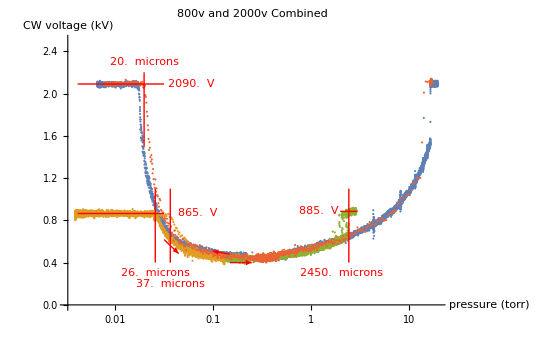

```mathematica
ListPlot[{pv4b,pv3a,pv3b,pv4a}, ScalingFunctions->{"Log",None},
PlotRange->{All,{0,2.5}},
Epilog->{Directive[{Red}],
p3=.026;Line[{{Log[p3],0.4},{Log[p3],1.1}}],
p4=.037;Line[{{Log[p4],0.4},{Log[p4],1.1}}],
p5=.020;Line[{{Log[p5],1.5},{Log[p5],2.2}}],
v2=.865;Line[{{Log[.0042],v2},{Log[.032],v2}}],
v5=2.09;Line[{{Log[.0042],v5},{Log[.032],v5}}],
Text[1000 p3" microns",{Log[p3],0.3}],
Text[1000 p4" microns",{Log[p4],0.2}],
Text[1000 p5" microns",{Log[p5],2.3}],
Text[1000 v2" V",{Log[.07],v2}],
p5=2.45;Line[{{Log[p5],0.4},{Log[p5],1.1}}],
v2=.885;Line[{{Log[2],v2},{Log[3],v2}}],
Text[1000 p5" microns",{Log[p5/1.2],0.3}],
Text[1000 v2" V",{Log[1.2],v2}],
Text[1000 v5" V",{Log[0.06],v5}],
Directive[Thick],
Arrow[{{Log[.15],0.4},{Log[.25],0.4}}],
Arrow[{{Log[.15],0.48},{Log[.10],0.51}}],
Arrow[{{Log[.032],0.68/1.1},{Log[.045],0.51/1.05}}]},
PlotLabel->"800v and 2000v Combined",
AxesLabel->{"pressure (torr)","CW voltage (kV)"}]
```

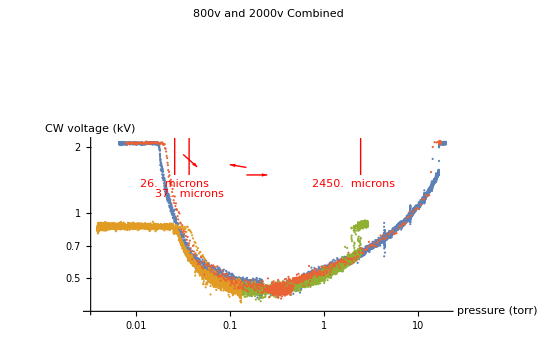

```mathematica
ListPlot[{pv4b,pv3a,pv3b,pv4a}, ScalingFunctions->{"Log","Log"},
PlotRange->{All,All},
Epilog->{Directive[{Red}],
p3=.026;Line[{{Log[p3],0.4},{Log[p3],1.1}}],
p4=.037;Line[{{Log[p4],0.4},{Log[p4],1.1}}],
p5=.020;Line[{{Log[p5],1.5},{Log[p5],2.2}}],
v2=.865;Line[{{Log[.0042],v2},{Log[.032],v2}}],
v5=2.09;Line[{{Log[.0042],v5},{Log[.032],v5}}],
Text[1000 p3" microns",{Log[p3],0.3}],
Text[1000 p4" microns",{Log[p4],0.2}],
Text[1000 p5" microns",{Log[p5],2.3}],
Text[1000 v2" V",{Log[.07],v2}],
p5=2.45;Line[{{Log[p5],0.4},{Log[p5],1.1}}],
v2=.885;Line[{{Log[2],v2},{Log[3],v2}}],
Text[1000 p5" microns",{Log[p5/1.2],0.3}],
Text[1000 v2" V",{Log[1.2],v2}],
Text[1000 v5" V",{Log[0.06],v5}],
Directive[Thick],
Arrow[{{Log[.15],0.4},{Log[.25],0.4}}],
Arrow[{{Log[.15],0.48},{Log[.10],0.51}}],
Arrow[{{Log[.032],0.68/1.1},{Log[.045],0.51/1.05}}]},
PlotLabel->"800v and 2000v Combined",
AxesLabel->{"pressure (torr)","CW voltage (kV)"}]
```

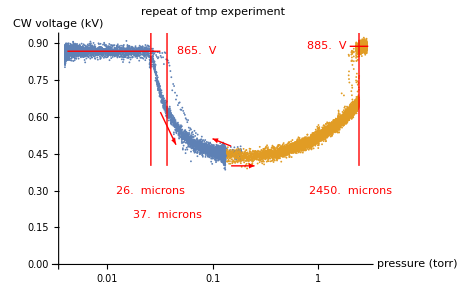

```mathematica
ListPlot[{pv3a,pv3b}, ScalingFunctions->{"Log",None},
Epilog->{Directive[{Red}],
p3=.026;Line[{{Log[p3],0.4},{Log[p3],1.1}}],
p4=.037;Line[{{Log[p4],0.4},{Log[p4],1.1}}],
v2=.865;Line[{{Log[.0042],v2},{Log[.032],v2}}],
Text[1000 p3" microns",{Log[p3],0.3}],
Text[1000 p4" microns",{Log[p4],0.2}],
Text[1000 v2" V",{Log[.07],v2}],
p5=2.45;Line[{{Log[p5],0.4},{Log[p5],1.1}}],
v2=.885;Line[{{Log[2],v2},{Log[3],v2}}],
Text[1000 p5" microns",{Log[p5/1.2],0.3}],
Text[1000 v2" V",{Log[1.2],v2}],
Directive[Thick],
Arrow[{{Log[.15],0.4},{Log[.25],0.4}}],
Arrow[{{Log[.15],0.48},{Log[.10],0.51}}],
Arrow[{{Log[.032],0.68/1.1},{Log[.045],0.51/1.05}}]},
PlotLabel->name3,
AxesLabel->{"pressure (torr)","CW voltage (kV)"}]
```

```mathematica
pirani3=GetDeviceData["PIRANI",jfile3];
```

```mathematica
pirani4=GetDeviceData["PIRANI",jfile4];
```

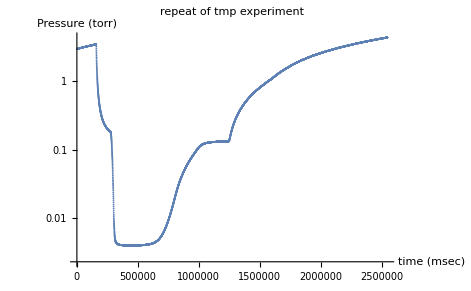

```mathematica
ListLogPlot[pirani3[[2,3]],PlotLabel->name3,
AxesLabel->{"time (msec)","Pressure (torr)"}]
```

```mathematica
intPressure3=Interpolation[pirani3[[2,3]]]
```

InterpolatingFunction[…]

```mathematica
intPressure4=Interpolation[pirani4[[2,3]]]
```

InterpolatingFunction[…]

```mathematica
pv4a=Table[{intPressure4[x[[1]]],-x[[2]]},{x,hv4a}];
```

```mathematica
pv4b=Table[{intPressure4[x[[1]]],-x[[2]]},{x,hv4b}];
```

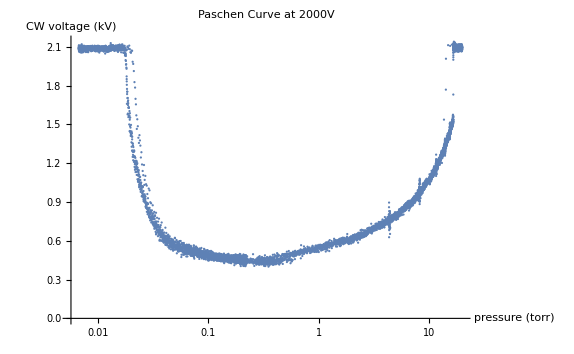

```mathematica
ListPlot[pv4a, ScalingFunctions->{"Log",None},PlotLabel->name4,
AxesLabel->{"pressure (torr)","CW voltage (kV)"}]
```

```mathematica
ColorData[1][6]
```

RGBColor[0.6, 0.24, 0.5632658430022722]

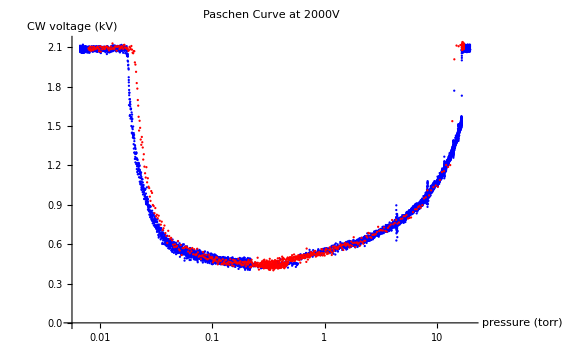

```mathematica
ListPlot[{pv4b,pv4a}, PlotStyle->{Blue,Red}, ScalingFunctions->{"Log",None},PlotLabel->name4,
AxesLabel->{"pressure (torr)","CW voltage (kV)"}]
```

```mathematica
pv3a=Table[{intPressure3[x[[1]]],-x[[2]]},{x,hv3a}];
```

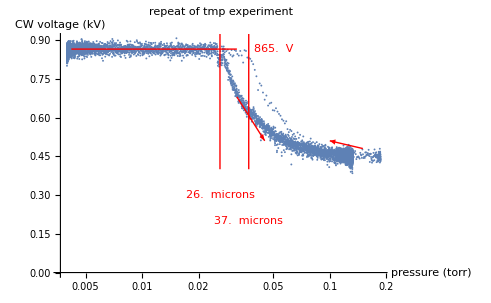

```mathematica
lp3a=ListPlot[pv3a, ScalingFunctions->{"Log",None},
Epilog->{Directive[{Red}],
p3=.026;Line[{{Log[p3],0.4},{Log[p3],1.1}}],
p4=.037;Line[{{Log[p4],0.4},{Log[p4],1.1}}],
v2=.865;Line[{{Log[.0042],v2},{Log[.032],v2}}],
Text[1000 p3" microns",{Log[p3],0.3}],
Text[1000 p4" microns",{Log[p4],0.2}],
Text[1000 v2" V",{Log[.05],v2}],
Directive[Thick],
Arrow[{{Log[.15],0.48},{Log[.10],0.51}}],
Arrow[{{Log[.032],0.68},{Log[.045],0.51}}]},
PlotLabel->name3,
AxesLabel->{"pressure (torr)","CW voltage (kV)"}]
```

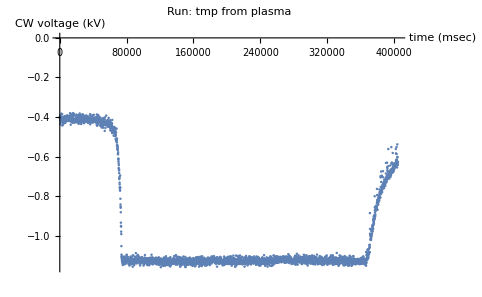

```mathematica
ListPlot[hv2[[2,1]],PlotLabel->"Run: tmp from plasma",
AxesLabel->{"time (msec)","CW voltage (kV)"}]
```

```mathematica
pirani2=GetDeviceData["PIRANI",jfile2];
```

```mathematica
pirani2[[1]]
```

{p2,p3,p4}

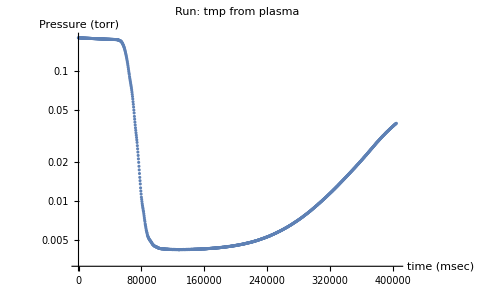

```mathematica
ListLogPlot[pirani2[[2,3]],PlotLabel->"Run: tmp from plasma",
AxesLabel->{"time (msec)","Pressure (torr)"}]
```

```mathematica
intPressure2=Interpolation[pirani2[[2,3]]]
```

InterpolatingFunction[…]

```mathematica
hv2[[2,1,-10;;]]
```

{{403600.56,-0.626374},{403718.53,-0.655388},{403837.5,-0.629828},{403956.48,-0.53864},{404075.45,-0.602195},{404193.42,-0.604268},{404312.4,-0.626374},{404431.37,-0.637427},{404550.34,-0.642954},{404669.31,-0.627065}}

```mathematica
pirani2[[2,3,-10;;]]
```

{{401283.33,0.03825},{401615.66,0.03832},{401958.01,0.03845},{402313.36,0.03865},{402655.71,0.03877},{402984.04,0.03896},{403326.39,0.03909},{403682.74,0.0393},{404026.09,0.03943},{404374.44,0.03958}}

```mathematica
pvList2=Table[{intPressure2[x[[1]]],-x[[2]]},{x,Drop[hv2[[2,1]],-10]}];
```

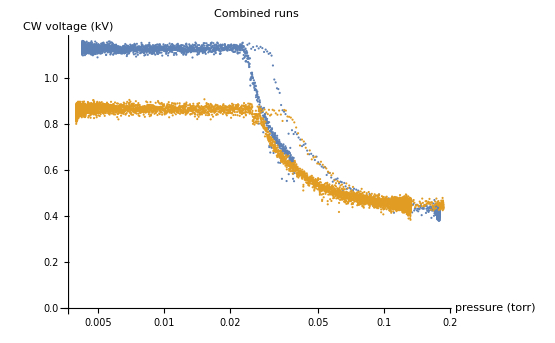

```mathematica
ListPlot[{pvList2,pv3a},ScalingFunctions->{"Log",None},
PlotLabel->"Combined runs",
AxesLabel->{"pressure (torr)","CW voltage (kV)"}]
```

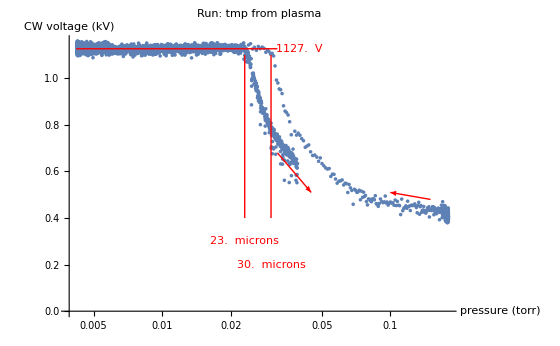

```mathematica
ListPlot[pvList2, ScalingFunctions->{"Log",None},
Epilog->{Directive[{Red}],
p3=.023;Line[{{Log[p3],0.4},{Log[p3],1.1}}],
p4=.030;Line[{{Log[p4],0.4},{Log[p4],1.1}}],
v2=1.127;Line[{{Log[.0042],v2},{Log[.032],v2}}],
Text[1000 p3" microns",{Log[p3],0.3}],
Text[1000 p4" microns",{Log[p4],0.2}],
Text[1000 v2" V",{Log[.04],v2}],
Directive[Thick],
Arrow[{{Log[.15],0.48},{Log[.10],0.51}}],
Arrow[{{Log[.032],0.68},{Log[.045],0.51}}]},
PlotLabel->"Run: tmp from plasma",
AxesLabel->{"pressure (torr)","CW voltage (kV)"}]
```

```mathematica
t1=138000;t2=162000;
```

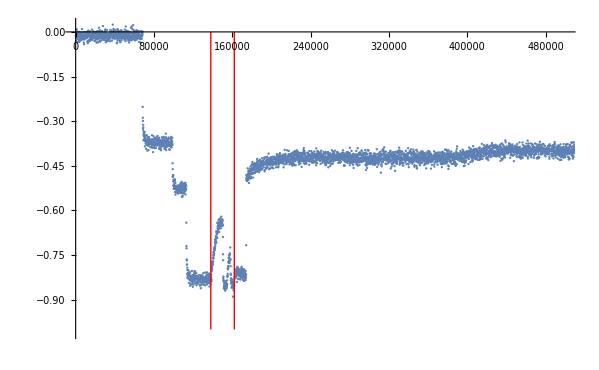

```mathematica
ListPlot[hv1[[2,1]],PlotRange->{{0,500000},All},
Epilog->{Directive[{Red}],Line[{{t1,-1},{t1,0}}],Line[{{t2,-1},{t2,0}}]}]
```

```mathematica
pirani1=GetDeviceData["PIRANI",jfile1];
```

```mathematica
pirani1[[1]]
```

{p2,p3,p4}

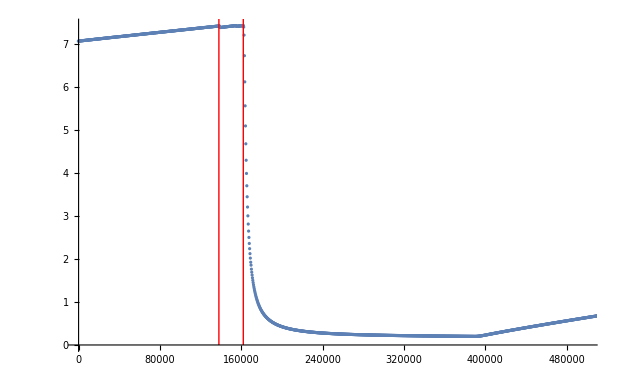

```mathematica
ListPlot[pirani1[[2,3]],PlotRange->{{0,500000},All},
Epilog->{Directive[{Red}],Line[{{t1,0},{t1,7.6}}],Line[{{t2,0},{t2,7.6}}]}]
```

```mathematica
variac1=GetDeviceData["VARIAC",jfile1];
```

```mathematica
variac1[[1]]
```

{dial_volts,input_volts,stop}

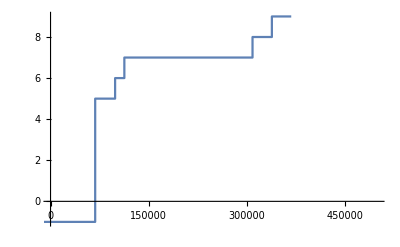

```mathematica
ListStepPlot[variac1[[2,2]],PlotRange->{{0,500000},All}]
```

```mathematica
command=GetDeviceData["Command",jfile];command[[1]]
```

{ip,observer,text}

```mathematica
MatrixForm[command[[2,3]]]
```

(5000. | variac:set:1
5000. | variac:set:1
10000. | variac:set:5
10000. | variac:set:5
20000. | variac:set:6
20000. | variac:set:6
46000. | variac:set:7
46000. | variac:set:7
140000. | RP on
391000. | variac:set:8
391000. | variac:set:8
418000. | variac:set:9
418000. | variac:set:9
491000. | RP off
1.68×10^6 | variac:set:0
1.68×10^6 | variac:set:0)

```mathematica
intPressure1=Interpolation[pirani1[[2,3]]]
```

InterpolatingFunction[…]

```mathematica
intPressure1[162000]
```

7.43706

```mathematica
intPressure1[163000]
```

6.88728

```mathematica
hv1[[2,1,1371]]
```

{161954.694,-0.842601}

```mathematica
<<Combinatorica`
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

```mathematica
BinarySearch[hv1[[2,1]],162000,#[[1]]&]//N
```

1371.5

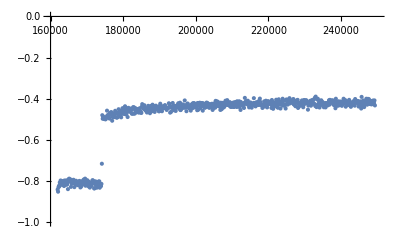

```mathematica
ListPlot[hv1[[2,1,1371;;2110]],PlotRange->{{160000,250000},{-1,0}}]
```

```mathematica
pvList=Table[{intPressure1[x[[1]]],-x[[2]]},{x,hv1[[2,1,1371;;2110]]}];
```

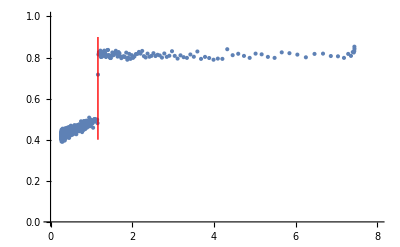

```mathematica
p1=1.16;ListPlot[pvList,PlotRange->{{0,8},{0,1}},Epilog->{Directive[{Red}],Line[{{p1,0.4},{p1,0.9}}]}]
```

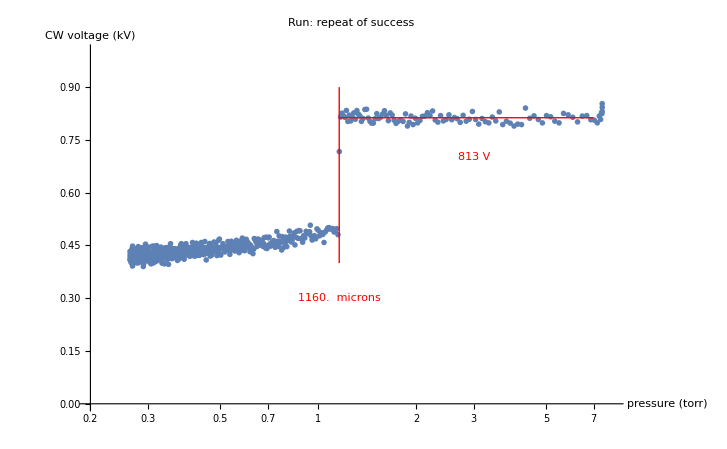

```mathematica
ListPlot[pvList, ScalingFunctions->{"Log",None},PlotRange->{{0.2,8},{0,1}},
Epilog->{Directive[{Red}],Line[{{Log[p1],0.4},{Log[p1],0.9}}],
Line[{{Log[p1],0.813},{Log[7],0.813}}],
Text[1000 p1" microns",{Log[p1],0.3}],
Text["813 V",{Log[3],0.7}]},
PlotLabel->"Run: repeat of success",
AxesLabel->{"pressure (torr)","CW voltage (kV)"}]
```

```mathematica
BinarySearch[Reverse[pvList],1.16,#[[1]]&]//N
```

636.5

```mathematica
Mean[pvList[[;;-638,2]]]
```

0.812896

```mathematica
command4
```

{{ip,observer,text},{{{56000.,10.20.82.127},{66000.,10.20.83.153},{73000.,10.20.83.153},{86000.,10.20.82.127},{91000.,10.20.82.127},{91000.,10.20.82.127},{100000.,10.20.82.127},{100000.,10.20.82.127},{140000.,10.20.82.127},{140000.,10.20.82.127},{140000.,10.20.82.127},{160000.,10.20.83.153},{160000.,10.20.83.153},{180000.,10.20.83.153},{180000.,10.20.83.153},{190000.,10.20.83.153},{190000.,10.20.83.153},{220000.,10.20.83.153},{220000.,10.20.83.153},{230000.,10.20.83.153},{230000.,10.20.83.153},{230000.,10.20.83.153},{290000.,10.20.83.153},{300000.,10.20.83.153},{300000.,10.20.83.153},{310000.,10.20.83.153},{310000.,10.20.83.153},{328000.,10.20.83.153},{328000.,10.20.83.153},{348000.,10.20.83.153},{380000.,10.20.83.153},{397000.,10.20.83.153},{440000.,10.20.83.153},{871000.,10.20.83.153}},{{56000.,gmein},{66000.,gfellows},{73000.,gfellows},{86000.,gmein},{91000.,gmein},{91000.,gmein},{100000.,gmein},{100000.,gmein},{140000.,gmein},{140000.,gmein},{140000.,gmein},{160000.,gfellows},{160000.,gfellows},{180000.,gfellows},{180000.,gfellows},{190000.,gfellows},{190000.,gfellows},{220000.,gfellows},{220000.,gfellows},{230000.,gfellows},{230000.,gfellows},{230000.,gfellows},{290000.,gfellows},{300000.,gfellows},{300000.,gfellows},{310000.,gfellows},{310000.,gfellows},{328000.,gfellows},{328000.,gfellows},{348000.,gfellows},{380000.,gfellows},{397000.,gfellows},{440000.,gfellows},{871000.,gfellows}},{{56000.,#promote: gfellows},{66000.,RP on},{73000.,RP off},{86000.,Solenoid open},{91000.,Set needle valve:50.0},{91000.,Set needle valve:50.0},{100000.,Set needle valve:100.0},{100000.,Set needle valve:100.0},{140000.,Solenoid closed},{140000.,Set needle valve:0.0},{140000.,Set needle valve:0.0},{160000.,variac:set:1.0},{160000.,variac:set:1.0},{180000.,variac:set:5.0},{180000.,variac:set:5.0},{190000.,variac:set:11.0},{190000.,variac:set:11.0},{220000.,variac:set:0.0},{220000.,variac:set:0.0},{230000.,Solenoid open},{230000.,Set needle valve:100.0},{230000.,Set needle valve:100.0},{290000.,Solenoid closed},{300000.,Set needle valve:0.0},{300000.,Set needle valve:0.0},{310000.,variac:set:5.0},{310000.,variac:set:5.0},{328000.,variac:set:10.0},{328000.,variac:set:10.0},{348000.,RP on},{380000.,TMP low},{397000.,TMP on},{440000.,TMP off},{871000.,RP off}}}}

```mathematica
rp4
```

{{rp_in},{{{-87182.4013,False},{66161.6646,True},{72625.4405,False},{347840.009,True},{871365.891,False}}}}